```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/subhajit/Dropbox/harmonics

```mathematica
hp2=-(1+c^2)Cos[2 psi]+x/6((19+9 c^2-2 c^4)-eta(19-11 c^2-6 c^4))Cos[2 psi];
```

```mathematica
hp4=-4/3 x s^2(1+c^2)(1-3 eta) Cos[4 psi];
```

```mathematica
hc2=-2 c Sin[2 psi]+(c x)/3((17-4 c^2)-eta (13-12 c^2))Sin[2 psi];
```

```mathematica
hc4=-8/3 x(1-3 eta)c s^2 Sin[4 psi];
```

```mathematica
G=6.674 10^-11;
```

```mathematica
c1=2.99792 10^8;
```

```mathematica
yr=3.154 10^7;
```

```mathematica
MS=1.989 10^30;
```

```mathematica
f1=10^-8.33;f2=10^-8.03;A1=10^-6.75;A2=10^-7.2;
```

```mathematica
omg=f1/2 2 Pi
```

1.46943×10^-8

```mathematica
psi=omg t
```

1.46943×10^-8 t

```mathematica
x=((G M MS omg)/c1^3)^(2/3)
```

1.73703×10^-9 M^(2/3)

```mathematica
eta=1/4;
```

```mathematica
(*theta=theta Pi/180;*)
(*M=1.5 10^13;*)
```

```mathematica
s=Sin[theta];c=Cos[theta];
```

```mathematica
sp2=Integrate[hp2,{t,0,10 yr}]
```

-5.27298×10^6+0.0217534 M^(2/3)+(-5.27298×10^6+0.017937 M^(2/3)) Cos[theta]^2-0.000763276 M^(2/3) Cos[theta]^4

```mathematica
sx2=Integrate[hc2,{t,0,10 yr}]
```

Cos[theta] (-1.35285×10^8+0.538527 M^(2/3)-0.0391656 M^(2/3) Cos[theta]^2)

```mathematica
sp4=Integrate[hp4,{t,0,10 yr}]
```

M^(2/3) (0.00301622 Sin[theta]^2+0.000754056 Sin[2 theta]^2)

```mathematica
sx4=Integrate[hc4,{t,0,10 yr}]
```

-0.000946254 M^(2/3) Cos[theta] Sin[theta]^2

```mathematica
(*1909-3744: Fp=0.15101656597630606;Fx=-0.6387878066821968*)
(*0613-0200: Fp=0.5409133848058575;Fx=-0.059939376031636606*)
```

```mathematica
Fp=0.15101656597630606;Fx=-0.6387878066821968
```

-0.638788

```mathematica
A1/A2
```

2.81838

```mathematica
ratio=(Fp sp2+Fx sx2)/(Fp sx4+Fx sx4)/.M->p^(3/2)//PowerExpand
```

1/p 2166.59 (-0.638788 Cos[theta] (-1.35285×10^8+0.538527 p-0.0391656 p Cos[theta]^2)+0.151017 (-5.27298×10^6+0.0217534 p+(-5.27298×10^6+0.017937 p) Cos[theta]^2-0.000763276 p Cos[theta]^4)) Csc[theta]^2 Sec[theta]

```mathematica
solve=Solve[ratio==A1/A2,p]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→-(1.05076×10^52 (5.09289×10^30-3.68467×10^32 Cos[theta]+1.69763×10^30 Cos[2. theta]))/(-2.05922×10^74+1.4586×10^76 Cos[theta]-5.80972×10^73 Cos[2. theta]-2.94789×10^74 Cos[3. theta]+6.45524×10^71 Cos[4. theta])}}

```mathematica
final=p^(3/2)/.solve[[1]]/.theta->theta1 Pi/180
```

1.0771×10^78 (-(5.09289×10^30+1.69763×10^30 Cos[0.0349066 theta1]-3.68467×10^32 Cos[(π theta1)/180])/(-2.05922×10^74-5.80972×10^73 Cos[0.0349066 theta1]-2.94789×10^74 Cos[0.0523599 theta1]+6.45524×10^71 Cos[0.0698132 theta1]+1.4586×10^76 Cos[(π theta1)/180]))^(3/2)

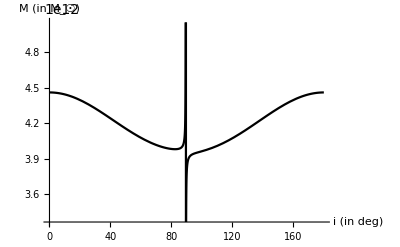

```mathematica
plot=Plot[final,{theta1,0, 180},PlotStyle->{Black},AxesLabel->{"i (in deg)","M (in M_☉)"}]
```

```mathematica
Export["Harmonics_siyuan_level2_1909-3744.pdf",plot,ImageResolution->500]
```

Harmonics_siyuan_level2_1909-3744.pdf

```mathematica
fisco=(c1^2/6)^(3/2)1/(2 Pi G)1/(4.5 10^12 MS)
```

4.8845×10^-10